```mathematica
Needs["NDSolve`FEM`"]
```

Generate mesh for a beam with a crack inside at given position.

```mathematica
generateMesh[crackX_, crackY_] := Module[{Ω, mesh},Ω = RegionDifference[Rectangle[{0,0},{200,20}],Ellipsoid[{crackX,crackY}, {10,2}]];
mesh=ToElementMesh[Ω, MaxCellMeasure->20];
Return[mesh];]
```

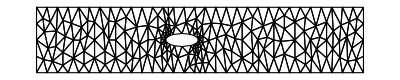

```mathematica
generateMesh[89, 10];
%["Wireframe"]
```

Define operator and boundary conditions.

```mathematica
op={({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive}/.{Y->12.7 10^4,ν->33/100};
```

```mathematica
Subscript[Γ, D]=DirichletCondition[{u[x,y]==0.,v[x,y]==0.},x==0];
```

Solve PDE for a given mesh.

```mathematica
solvePDE[mesh_]:=NDSolveValue[{op=={0,NeumannValue[-40,x==200]},Subscript[Γ, D]},{u,v},{x, y}∈mesh];
```

Show pictures for given mesh and solution.

```mathematica
showPic[mesh_, sol_]:=Show[{mesh["Wireframe"["MeshElement"-> "BoundaryElements"]],
ElementMeshDeformation[mesh, sol]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]}];
showDiagram[mesh_,sol_]:=ContourPlot[sol[[1]][x,y], {x, y}∈mesh, ColorFunction->"Temperature", AspectRatio->Automatic]
```

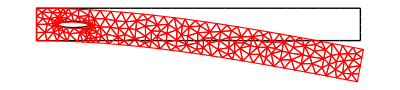

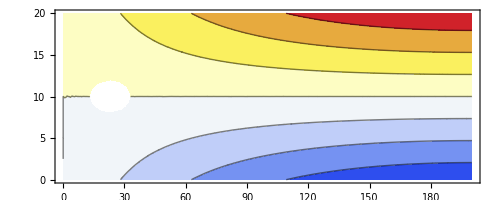

```mathematica
m=generateMesh[23, 10];
sol=solvePDE[m];
showPic[m,sol]
showDiagram[m,sol]
```

Print and export sensors readings.

```mathematica
points = Table[{x, sol[[1]][x, 20]}, {x, Range[0, 200, 20]}]
```

{{0,0.},{20,0.369111},{40,0.68077},{60,0.963997},{80,1.20966},{100,1.41755},{120,1.58762},{140,1.71991},{160,1.8144},{180,1.87107},{200,1.89106}}

```mathematica
If[!DirectoryQ["Mathematica_Export"], CreateDirectory["Mathematica_Export"]]
```

```mathematica
Export["~/Mathematica_Export/test.txt", points, "Table"]
```

~/Mathematica_Export/test.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["~/Mathematica_Export/test.txt"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["~/Mathematica_Export/test.txt"]]]
```

Export sensors readings in the cycle.

```mathematica
If[FileExistsQ["~/Mathematica_Export/output.txt"], DeleteFile["~/Mathematica_Export/output.txt"]]
str = File[CreateFile["~/Mathematica_Export/output.txt"]]
WriteString[str, "exp_number crackX crackY sensor0 sensor1 sensor2 sensor3 sensor4 sensor5 sensor6 sensor7 sensor8 sensor9 sensor10\n"];
For[i=0,i<10,i++,{
crackX = 10 + RandomReal[{0, 180}];
crackY = 2 + RandomReal[{0, 16}];
m = generateMesh[crackX, crackY];
sol = solvePDE[m];
WriteString[str, i, " ", crackX, " ", crackY, " ", StringRiffle[Table[sol[[1]][x, 20], {x, 0, 200, 20}]]];
WriteString[str, "\n"]
}]
Close[str]
```

File[/Users/admishchenko/Mathematica_Export/output.txt]

/Users/admishchenko/Mathematica_Export/output.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/Users/admishchenko/Mathematica_Export/output.txt"]]]
```